```mathematica
SetDirectory[NotebookDirectory[]<>"\\MethodsODE\\OutputData\\"]
```

D:\BMSTU\3 COURSE\6th term\Numeric Methods\Lab1\methodsODE\MethodsODE\OutputData

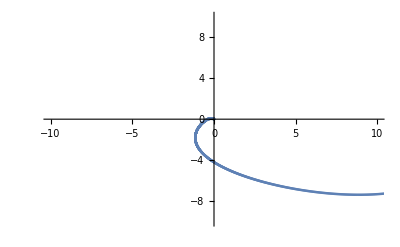

```mathematica
data1 = Import["simScheme-1", "Table"]
pl1=ListPlot[Table[data1[[i]],{i,2, Length[data1],2}],PlotRange->{{-10,10},{-10,10}}]
```

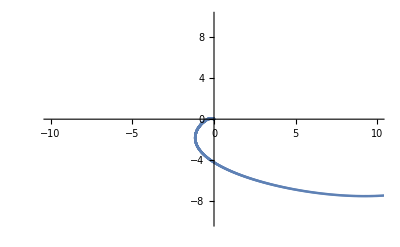

```mathematica
data2 = Import["eulersimple-1", "Table"];
pl3=ListPlot[Table[data2[[i]],{i,2, Length[data2],2}],PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
sol1 = Expand@DSolve[{x'[t]==2x[t]+(y[t])^2-1, y'[t]==6x[t]-(y[t])^2+1, x[0]==0,y[0]==0},{x[t],y[t]},{t,0,2}]
```

DSolve[{x'[t]==-1+2 x[t]+y[t]^2,y'[t]==1+6 x[t]-y[t]^2,x[0]==0,y[0]==0},{x[t],y[t]},{t,0,2}]

```mathematica
pl2=ParametricPlot[{x[t],y[t]}/.sol1, {t,0,2},PlotStyle->Orange,PlotRange->{{-10,10},{-10,10}}]
```

DSolve::alliv: The function x[0.0000408163] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

ReplaceAll::reps: {DSolve[{x'[0.0000408163]==-1+2 x[0.0000408163]+y[0.0000408163]^2,y'[0.0000408163]==1+6 x[0.0000408163]-y[«1»]^2,x[0]==0,y[0]==0},{x[0.0000408163],y[0.0000408163]},{0.0000408163,0,2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000408163 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.0000408163]==-1.+2. x[0.0000408163]+y[0.0000408163]^2,y'[0.0000408163]==1.+6. x[0.0000408163]-1. y[«1»]^2,x[0.]==0.,y[0.]==0.},{x[0.0000408163],y[0.0000408163]},{0.0000408163,0.,2.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::alliv: The function x[0.0408571] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

ReplaceAll::reps: {DSolve[{x'[0.0408571]==-1+2 x[0.0408571]+y[0.0408571]^2,y'[0.0408571]==1+6 x[0.0408571]-y[«1»]^2,x[0]==0,y[0]==0},{x[0.0408571],y[0.0408571]},{0.0408571,0,2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.0408571 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

DSolve::alliv: The function x[0.0816735] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

General::stop: Further output of DSolve::alliv will be suppressed during this calculation.

-Graphics-

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

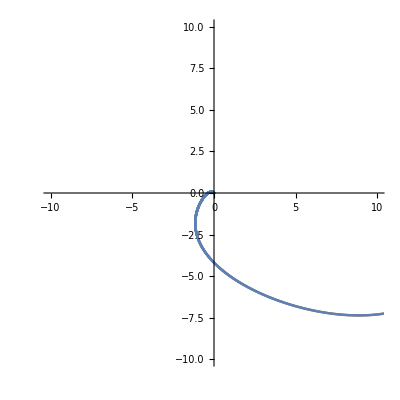

```mathematica
Show[pl2,pl1]
```

```mathematica
(*система 1*)
```